Part 5

```mathematica
meanField2[J_,epsilon_,flag_]:=(
mOld={1,-1,-1,-1,-1,-1,1};mWorking={1,-1,-1,-1,-1,-1,1};
If[flag==1,mOld={1,1,1,1,1,1,1};mWorking={1,1,1,1,1,1,1}];
(*Print[mWorking];*)
conv=0;
iteration=0;
While[conv==0,
maxDiff=0; 
iteration++;
(*Print["iteration ",iteration];*)
For[i=2,i≤6,i++,
mOld[[i]]=mWorking[[i]];
hi=(4*epsilon-J*(mWorking[[i+1]]+mWorking[[i-1]]));
(*Print["  spin # ",i-1," hi = ",hi," mWorking[[i-1]] = ",mWorking[[i-1]], " mWorking[[i+1]] = ",mWorking[[i+1]]];*)
mWorking[[i]]=(-1*Exp[hi]+Exp[-1*hi])/(Exp[-1*hi]+Exp[hi]);
maxDiff=Max[Abs[mOld[[i]]-mWorking[[i]]],maxDiff];
(*Print["   new m = ",mWorking[[i]]," diff = ",Abs[mOld[[i]]-mWorking[[i]]]];*)
]
If[maxDiff<0.000001,conv=1];
];
finalSpins = {mWorking[[2]],mWorking[[3]],mWorking[[4]],mWorking[[5]],mWorking[[6]]};
Return[mWorking];
)
```

```mathematica
fromMeanField[J_,epsilon_,avgSpins_]:=(
ClearAll[PofN, numerators, energies, Ns, spins, counter];
counter=0;
(*J=0.4;
epsilon=0.2;*)
Ns=ConstantArray[0,{32}];
energies=ConstantArray[0,{32}];
spins={0,0,0,0,0};
numerators={0,0,0,0,0,0};
PofN={{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}};
Q=0;
For[i=-1,i≤1,i+=2,
	For[j=-1,j≤1,j+=2,
		For[k=-1,k≤1,k+=2,
			For[l=-1,l≤1,l+=2,
				For[m=-1,m≤1,m+=2,
				(*Print[i ,j, k, l, m];*)
					spins[[1]]=i;
					spins[[2]]=j; 
					spins[[3]]=k;
					spins[[4]]=l;
					spins[[5]]=m;
					counter++;
					etot=0;
					For[u=1,u≤5,u++,
						etot+= spins[[u]]*(4*epsilon-J*(avgSpins[[u]]+avgSpins[[u+2]]));
						Ns[[counter]]+=(spins[[u]]+1)/2;
					];
					(*Print[spins," total energy = ",etot];*)
					energies[[counter]]=etot
				];
		];
	];
];
];
For[z=1,z≤32,z++,
(*Print[z,"      ",       energies[[z]],"    ",Exp[-1*energies[[z]]],"   ",Q];*)
Q+=Exp[-1*energies[[z]]];
numerators[[Ns[[z]]+1]]+=Exp[-1*energies[[z]]];
(*Print[energies[[z]]];*)
];
For[q=1,q≤6,q++,
PofN[[q]][[2]]=numerators[[q]]/Q;
];
Return[PofN];
)
```

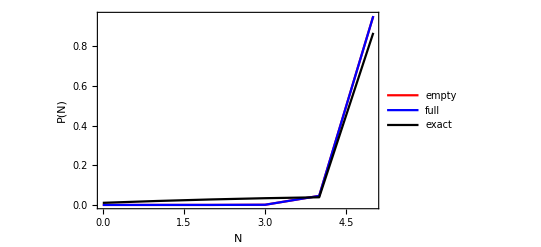

```mathematica
fig6=ListLinePlot[{fromMeanField[1.2,0.01,meanField2[1.2,0.01,-1]],fromMeanField[1.2,0.01,meanField2[1.2,0.01,1]],getDist[1.2,0.01,1]},Frame->True,FrameLabel->{"N","P(N)"},PlotStyle->{Red, Blue,Black},PlotLegends->{"empty","full","exact"},BaseStyle->{FontSize->14},PlotRange->All]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig6.eps",fig6]
```

/Users/rachelkrueger/Documents/StatMech/fig6.eps

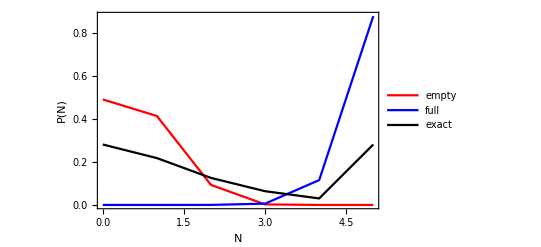

```mathematica
fig7=ListLinePlot[{fromMeanField[1.2,0.12,meanField2[1.2,0.12,-1]],fromMeanField[1.2,0.12,meanField2[1.2,0.12,1]],getDist[1.2,0.12,1]},Frame->True,FrameLabel->{"N","P(N)"},PlotStyle->{Red, Blue,Black},BaseStyle->{FontSize->14},PlotLegends->{"empty","full","exact"}]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig7.eps",fig7]
```

/Users/rachelkrueger/Documents/StatMech/fig7.eps

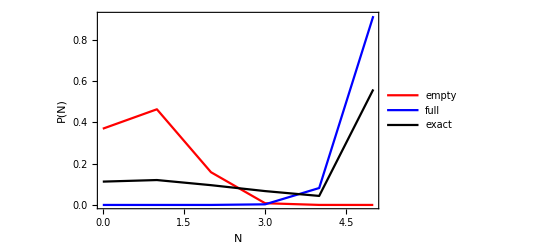

```mathematica
fig8=ListLinePlot[{fromMeanField[1.2,0.08,meanField2[1.2,0.08,-1]],fromMeanField[1.2,0.08,meanField2[1.2,0.08,1]],getDist[1.2,0.08,1]},Frame->True,FrameLabel->{"N","P(N)"},PlotStyle->{Red, Blue,Black},BaseStyle->{FontSize->14},PlotLegends->{"empty","full","exact"}]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig8.eps",fig8]
```

/Users/rachelkrueger/Documents/StatMech/fig8.eps

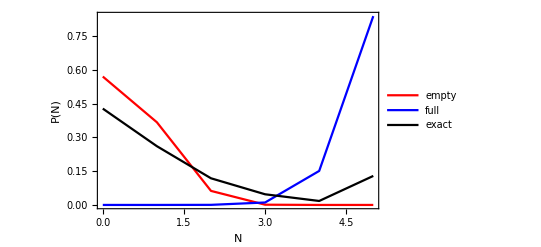

```mathematica
fig12=ListLinePlot[{fromMeanField[1.2,0.15,meanField2[1.2,0.15,-1]],fromMeanField[1.2,0.15,meanField2[1.2,0.15,1]],getDist[1.2,0.15,1]},Frame->True,FrameLabel->{"N","P(N)"},PlotStyle->{Red, Blue,Black},BaseStyle->{FontSize->14},PlotLegends->{"empty","full","exact"}]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig12.eps",fig12]
```

/Users/rachelkrueger/Documents/StatMech/fig12.eps

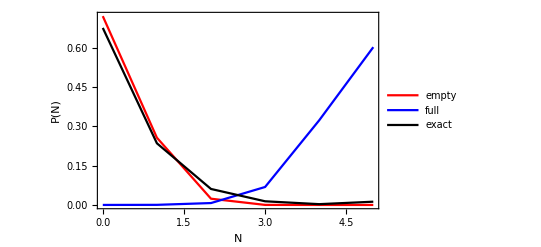

```mathematica
fig13=ListLinePlot[{fromMeanField[1.2,0.22,meanField2[1.2,0.22,-1]],fromMeanField[1.2,0.22,meanField2[1.2,0.22,1]],getDist[1.2,0.22,1]},Frame->True,FrameLabel->{"N","P(N)"},PlotStyle->{Red, Blue,Black},BaseStyle->{FontSize->14},PlotLegends->{"empty","full","exact"}]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig13.eps",fig13]
```

/Users/rachelkrueger/Documents/StatMech/fig13.eps

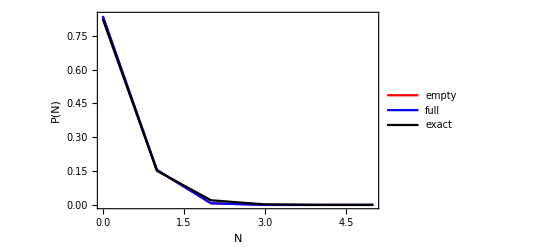

```mathematica
fig14=ListLinePlot[{fromMeanField[1.2,0.3,meanField2[1.2,0.3,-1]],fromMeanField[1.2,0.3,meanField2[1.2,0.3,1]],getDist[1.2,0.3,1]},Frame->True,FrameLabel->{"N","P(N)"},PlotStyle->{Red, Blue,Black},BaseStyle->{FontSize->14},PlotLegends->{"empty","full","exact"},PlotRange->All]
```

```mathematica
Export["/Users/rachelkrueger/Documents/StatMech/fig14.eps",fig14]
```

/Users/rachelkrueger/Documents/StatMech/fig14.eps